# QKT D₂ Plot

## Classical Kicked Top

```mathematica
ClassicalToSphere = Compile[{{q, _Real, 1}},
  Module[{b2 = q[[1]]^2 + q[[2]]^2},
    {q[[1]] Sqrt[1 - 0.25 b2], q[[2]] Sqrt[1 - 0.25 b2], 0.5 b2 - 1.0}
  ], CompilationTarget -> "C"];
(* disk center (r=0) -> sz=+1 = north pole; border (r=2) -> sz=-1 = south pole *)

ClassicalToDisk = Compile[{{s, _Real, 1}},
  Module[{b = Sqrt[2.0 / (1.0 - s[[3]])]},
    {s[[1]] b, s[[2]] b}
  ], CompilationTarget -> "C"];
(* inverse of ClassicalToSphere; singular at south pole (sz=-1) *)

ClassicalStep = Compile[
  {{s, _Real, 1}, {alpha, _Real}, {k, _Real}, {order, _Integer}},
  Module[{sx = s[[1]], sy = s[[2]], sz = s[[3]],
          ca = Cos[alpha], sa = Sin[alpha], sxc, sxs, r1, r2, r3},
    If[order == 0,
      (* rotation-kick *)
      r1 = ca sx - sa sy; r2 = sa sx + ca sy; r3 = sz;
      sx = r1; sy = r2; sz = r3;
      sxc = Cos[k sx]; sxs = Sin[k sx];
      r1 = sx; r2 = sxc sy - sxs sz; r3 = sxs sy + sxc sz;,
      (* kick-rotation *)
      sxc = Cos[k sx]; sxs = Sin[k sx];
      r1 = sx; r2 = sxc sy - sxs sz; r3 = sxs sy + sxc sz;
      sx = r1; sy = r2; sz = r3;
      r1 = ca sx - sa sy; r2 = sa sx + ca sy; r3 = sz;
    ];
    {r1, r2, r3}
  ], CompilationTarget -> "C"];

ClassicalMapeo = Compile[
  {{qini, _Real, 1}, {alpha, _Real}, {k, _Real},
   {n, _Integer}, {order, _Integer}},
  Module[{s, traj},
    s = ClassicalToSphere[qini];
    traj = Table[
      s = ClassicalStep[s, alpha, k, order];
      ClassicalToDisk[s], {n}];
    traj
  ],
  CompilationTarget -> "C",
  CompilationOptions -> {"InlineCompiledFunctions" -> True},
  RuntimeAttributes -> {Listable}, RuntimeOptions -> "Speed"
];
```

## Spin Operators

```mathematica
ClearAll[sz, sp, sm, sx, sx2];
(* Sz: diagonal {+j, j-1, ..., -j} *)
sz[j_] := sz[j] = SparseArray[Band[{1, 1}] -> Range[j, -j, -1]];
(* S+: superdiagonal; element (i, i+1) = <m_i|S+|m_{i+1}> with m_i = j-i+1 *)
sp[j_] := sp[j] = SparseArray[Band[{1, 2}] ->
    Table[Sqrt[j (j + 1) - m (m + 1)] // N, {m, j - 1, -j, -1}],
    {2 j + 1, 2 j + 1}];
(* S-: subdiagonal; transpose of S+ *)
sm[j_] := sm[j] = SparseArray[Band[{2, 1}] ->
    Table[Sqrt[j (j + 1) - m (m - 1)] // N, {m, j, -j + 1, -1}],
    {2 j + 1, 2 j + 1}];
sx[j_]  := sx[j]  = (1/2) (sp[j] + sm[j]);
sx2[j_] := sx2[j] = sx[j] . sx[j];
```

## Spin Coherent State Compiler

```mathematica
Clear[generateCoherentStateCompiler];
generateCoherentStateCompiler = Compile[{{J, _Integer}, {q, _Real}, {p, _Real}},
  Module[{dim, zeta, result, mVals, logs, maxLog, terms, norm, r2},
    dim = 2 J + 1;
    result = ConstantArray[0.0 + 0. I, dim];
    r2 = q^2 + p^2;
    If[r2 >= 4.0,
      result[[1]] = 1.0 + 0. I,            (* north pole: m=+J, index 1, at border *)
      zeta = (q - I p) / Sqrt[4 - r2];    (* conjugate: south-pole param -> north at center *)
      If[Abs[zeta] == 0.0,
        result[[dim]] = 1.0 + 0. I,        (* south pole: m=-J, index dim, at center *)
        mVals = Range[J, -J, -1];          (* descending: J, J-1, ..., -J *)
        logs = 0.5 (LogGamma[2 J + 1] - LogGamma[J + 1 + mVals] -
                    LogGamma[J + 1 - mVals]) + (J + mVals) Log[zeta];
        maxLog = Max[Re[logs]];
        terms  = Exp[logs - maxLog];
        norm   = Sqrt[Total[Abs[terms]^2]];
        result = terms / norm;
      ]
    ];
    result
  ],
  CompilationTarget -> "WVM", RuntimeOptions -> "Speed",
  Parallelization -> True, RuntimeAttributes -> {Listable}
];
```

## Floquet Operator

```mathematica
kickPart[j_, k_]    := MatrixExp[(-I k / (2 j)) sx2[j]];
freePart[j_, alpha_] := SparseArray[Band[{1, 1}] -> Exp[-I alpha Range[j, -j, -1]]];
Floq[j_, alpha_, k_] := kickPart[j, k] . freePart[j, alpha];
Floqsym[j_, alpha_, k_] :=freePart[j, alpha/2]. kickPart[j, k] . freePart[j, alpha/2];
```

### Parity Decomposition

```mathematica
(* Sx^2 couples m to m +/- 2, so alternating array indices always decouple.
   Odd integer j: index 1 has m=j (odd), so Even-m sector starts at index 2.
   Even integer j or half-integer j: index 1 starts the first sector. *)
ParitySectorIndices[j_] :=
  Module[{d = 2 j + 1},
    If[IntegerQ[j] && OddQ[j],
      <|"Even" -> Range[2, d, 2], "Odd" -> Range[1, d, 2]|>,
      <|"Even" -> Range[1, d, 2], "Odd" -> Range[2, d, 2]|>
    ]
  ];
```

```mathematica
GetQKTParityEigensystem[jParam_, alphaParam_, kParam_] :=
  Module[{mat, d, idx, matEven, matOdd, esEven, esOdd,
          phEven, phOdd, vecsEven, vecsOdd, idxE, idxO,
          fullVecsEven, fullVecsOdd},
mat = Floq[jParam, alphaParam, kParam];
d = 2 jParam + 1;
idx = ParitySectorIndices[jParam];
matEven = mat[[idx["Even"], idx["Even"]]];
matOdd  = mat[[idx["Odd"], idx["Odd"]]];
esEven = Eigensystem[matEven, Method -> "Direct"];
esOdd  = Eigensystem[matOdd, Method -> "Direct"];
phEven = Mod[Arg[esEven[[1]]], 2 Pi];
phOdd  = Mod[Arg[esOdd[[1]]], 2 Pi];
idxE = Ordering[phEven]; 
idxO = Ordering[phOdd];
vecsEven = esEven[[2, idxE]];
vecsOdd  = esOdd[[2, idxO]];
    
fullVecsEven = Table[
Module[{vec = ConstantArray[0. + 0. I, d]},
        vec[[idx["Even"]]] = vecsEven[[i]]; vec],
      {i, Length[idx["Even"]]}];

    fullVecsOdd = Table[
Module[{vec = ConstantArray[0. + 0. I, d]},
        vec[[idx["Odd"]]] = vecsOdd[[i]]; vec],
      {i, Length[idx["Odd"]]}];

    <|"Even" -> <|"Quasienergies" -> esEven[[1]],
"FullVectors" -> fullVecsEven|>,
      "Odd"  -> <|"Quasienergies" -> esOdd[[1]],
"FullVectors" -> fullVecsOdd|>|>
  ];
```

## Parameters

```mathematica
α = Pi/2.;
k = 3.0;
(* Quantum *)
J = 1000;
d = 2 J + 1;
(* Phase-space grid *)
radius = 2;
delta  = 0.020;
```

```mathematica
(* Classical Poincare *)
kicks  = 1500;
points = 1000;
```

## Classical Poincare Section

```mathematica
randomregion  = RandomPoint[Disk[{0, 0}, 1.99], points];
classicalTraj = ClassicalMapeo[randomregion, α, k, kicks, 0];
poincarePoints = ArrayReshape[classicalTraj, {points kicks, 2}];

poincare = ListPlot[poincarePoints,
  PlotStyle  -> Directive[PointSize[0.0005], Black, Opacity[0.15]],
  Frame      -> True, Axes -> True,
  GridLines  -> Automatic,
  PlotRange  -> {{-2, 2}, {-2, 2}},
  FrameLabel -> {Style["Q", 30, Black], Rotate[Style["P", 30, Black], -90 Degree]},
  LabelStyle -> Directive[30, Black],
  AspectRatio -> 1,
  ImageSize  -> 1000];
```

## Grid Over Disk

```mathematica
gridPointsRaw = Flatten[Table[{x, y},
  {x, Range[-radius, radius, delta]},
  {y, Range[-radius, radius, delta]}], 1];
region = Select[gridPointsRaw, Norm[#] < radius &];
Print["Grid points: ", Length[region]];
```

Grid points: 31397

## Coherent States

```mathematica
SetDirectory[NotebookDirectory[]];
LaunchKernels[12];
```

```mathematica
Print["Generating coherent states over ", Length[region], " points..."];
statesCompiled = ParallelMap[
  generateCoherentStateCompiler[J, #[[1]], #[[2]]] &,
  region, Method -> "CoarsestGrained"];
```

Generating coherent states over 31397 points...

## Floquet Eigensystem — Parity Decomposition

```mathematica
(* Similarity transform: mat = exp(-i alpha Sz) . Floq . exp(i alpha Sz)
   = exp(-i alpha Sz) . exp(-ik/(2J) Sx^2)
   Sx^2 couples m to m+-2 only, so odd/even indices decouple in mat. *)
Print["Building Floquet matrix..."];
data=GetQKTParityEigensystem[J,α,k];
```

Building Floquet matrix...

```mathematica
eigenvecM=data["Even","FullVectors"];
eigenvecm=data["Odd","FullVectors"];
neweigenvec=Riffle[eigenvecM,eigenvecm];
```

## Overlaps and D2

```mathematica
Print["Projecting coherent states into Floquet basis..."];
overlaps  = Conjugate[neweigenvec] . Transpose[statesCompiled];

Print["Computing IPR..."];
iprValues = Total[Abs[overlaps]^4, {1}];

(* D2 = -log(IPR) / log(d),  d = 2J+1 *)
d2Values  = -Log[iprValues] / Log[d];
```

Projecting coherent states into Floquet basis...

Computing IPR...

## D2 Density Plot + Poincare Overlay

```mathematica
d2plot = ListDensityPlot[
  Transpose[{region[[All, 1]], region[[All, 2]], d2Values}],
  PlotRange     -> All,
  PlotTheme     -> "Detailed",
  ColorFunction -> "SunsetColors",
  PlotLabel     -> Style[
    "D₂, J = " <> ToString[J] <>
    ", α = " <> ToString[N[α]] <>
    ", k = " <> ToString[NumberForm[k, {4, 2}]], 25, Black],
  ImageSize     -> 1000,
  FrameLabel    -> {Style["Q", 40, Black], Rotate[Style["P", 40, Black], -90 Degree]},
  LabelStyle    -> Directive[30, Black],
  AspectRatio   -> 1,
  Frame         -> True,
  InterpolationOrder -> 3];

overlay = Show[{d2plot, poincare}];

Export[
  "north_D2_J_" <> ToString[J] <>
  "_alpha_" <> StringReplace[ToString[N[α]], "." -> "p"] <>
  "_k_" <> StringReplace[ToString[k], "." -> "p"] <> ".png",
  overlay, ImageResolution -> 200]
```

north_D2_J_1000_alpha_1p5708_k_3p.png

# IPR statistics

## Floquet Operator

### Parity Decomposition

```mathematica
GetQKTParityEigensystemsym[jParam_, alphaParam_, kParam_] :=
  Module[{mat, d, idx, matEven, matOdd, esEven, esOdd,
          phEven, phOdd, vecsEven, vecsOdd, idxE, idxO,
          fullVecsEven, fullVecsOdd},

mat = Floqsym[jParam, alphaParam, kParam];
d = 2 jParam + 1;
idx = ParitySectorIndices[jParam];
matEven = mat[[idx["Even"], idx["Even"]]];
matOdd  = mat[[idx["Odd"], idx["Odd"]]];
esEven = Eigensystem[matEven, Method -> "Direct"];
esOdd  = Eigensystem[matOdd, Method -> "Direct"];
phEven = Mod[Arg[esEven[[1]]], 2 Pi];
phOdd  = Mod[Arg[esOdd[[1]]], 2 Pi];
idxE = Ordering[phEven]; 
idxO = Ordering[phOdd];
vecsEven = esEven[[2, idxE]];
vecsOdd  = esOdd[[2, idxO]];
    
fullVecsEven = Table[
Module[{vec = ConstantArray[0. + 0. I, d]},
        vec[[idx["Even"]]] = vecsEven[[i]]; vec],
      {i, Length[idx["Even"]]}];

    fullVecsOdd = Table[
Module[{vec = ConstantArray[0. + 0. I, d]},
        vec[[idx["Odd"]]] = vecsOdd[[i]]; vec],
      {i, Length[idx["Odd"]]}];

    <|"Even" -> <|"Quasienergies" -> esEven[[1]],
"FullVectors" -> fullVecsEven|>,
      "Odd"  -> <|"Quasienergies" -> esOdd[[1]],
"FullVectors" -> fullVecsOdd|>|>
  ]
```

## Parameters

```mathematica
α = Pi/2.;
k = 3.;
(* Quantum *)
J = 1000;
d = 2 J + 1;
(* Phase-space grid *)
radius = 2;
delta  = 0.020;
```

## Grid Over Disk

```mathematica
gridPointsRaw = Flatten[Table[{x, y},
  {x, Range[-radius, radius, delta]},
  {y, Range[-radius, radius, delta]}], 1];
region = Select[gridPointsRaw, Norm[#] < radius &];
Print["Grid points: ", Length[region]];
```

Grid points: 31397

## Coherent States

```mathematica
SetDirectory[NotebookDirectory[]];
LaunchKernels[12];
```

```mathematica
Print["Generating coherent states over ", Length[region], " points..."];
statesCompiled = ParallelMap[
  generateCoherentStateCompiler[J, #[[1]], #[[2]]] &,
  region, Method -> "CoarsestGrained"];
```

Generating coherent states over 31397 points...

## Floquet Eigensystem — Parity Decomposition

```mathematica
(* Similarity transform: mat = exp(-i alpha Sz) . Floq . exp(i alpha Sz)
   = exp(-i alpha Sz) . exp(-ik/(2J) Sx^2)
   Sx^2 couples m to m+-2 only, so odd/even indices decouple in mat. *)
Print["Building Floquet matrix..."];
data=GetQKTParityEigensystem[J,α,k];
datasym=GetQKTParityEigensystemsym[J,α,k];
```

Building Floquet matrix...

```mathematica
eigenvecM=data["Even","FullVectors"];
eigenvecm=data["Odd","FullVectors"];
neweigenvec=Riffle[eigenvecM,eigenvecm];
eigenvecMsym=datasym["Even","FullVectors"];
eigenvecmsym=datasym["Odd","FullVectors"];
neweigenvecsym=Riffle[eigenvecMsym,eigenvecmsym];
```

## Overlaps and D2

```mathematica
Print["Projecting coherent states into Floquet basis..."];
overlaps  = Conjugate[neweigenvec] . Transpose[statesCompiled];
overlapsym  = Conjugate[neweigenvecsym] . Transpose[statesCompiled];

Print["Computing IPR..."];
iprValues = Total[Abs[overlaps]^4, {1}];
iprValuesym = Total[Abs[overlapsym]^4, {1}];

(* D2 = -log(IPR) / log(d),  d = 2J+1 *)
d2Values  = -Log[iprValues] / Log[d];
d2Valuesym  = -Log[iprValuesym] / Log[d];
```

Projecting coherent states into Floquet basis...

Computing IPR...

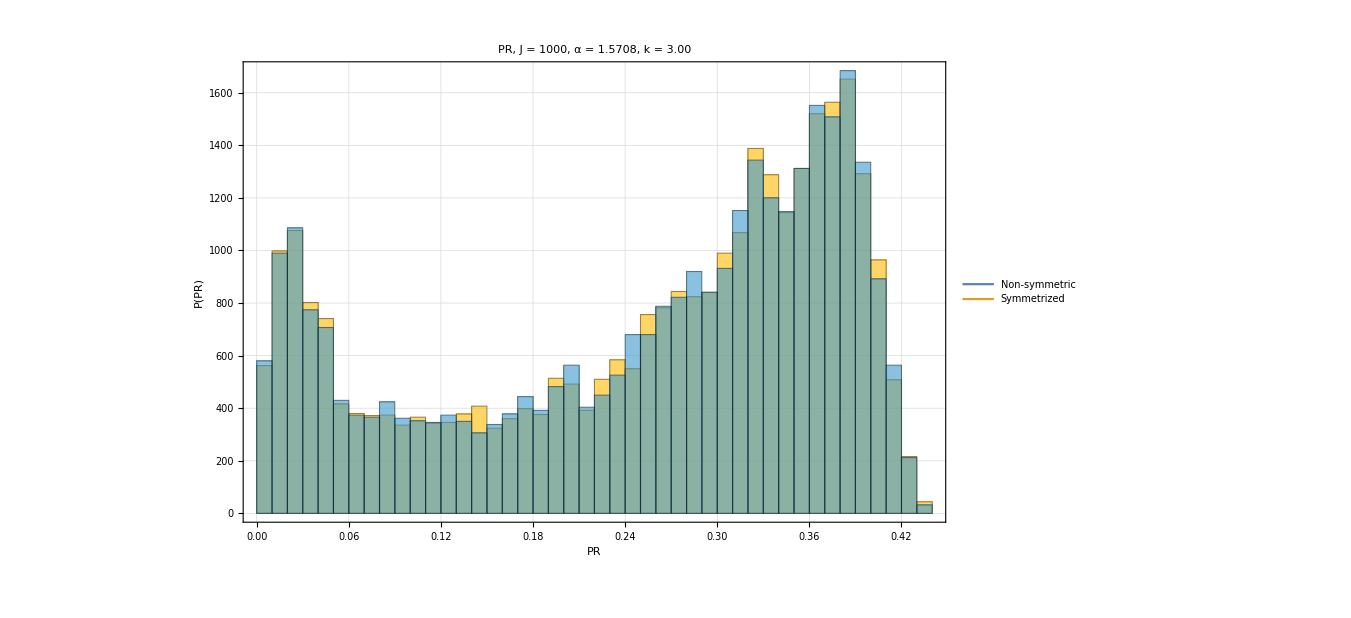

```mathematica
Legended[Histogram[{(1/iprValues)(1/d),(1/iprValuesym)(1/d)},
50,
PlotTheme->"Detailed",
PlotLabel     -> Style[
    "PR, J = " <> ToString[J] <>
    ", α = " <> ToString[N[α]] <>
    ", k = " <> ToString[NumberForm[k, {4, 2}]], 25, Black],
FrameLabel    -> {Style["PR", 40, Black], Rotate[Style["P(PR)", 40, Black], -90 Degree]},
  LabelStyle    -> Directive[30, Black],
ImageSize->1000,PlotRange->All],
Placed[LineLegend[{ColorData[97][1],ColorData[97][2]},{"Non-symmetric","Symmetrized"}],{0.6,0.9}]]
```

```mathematica
d2plotsym= ListDensityPlot[
  Transpose[{region[[All, 1]], region[[All, 2]], d2Valuesym}],
  PlotRange     -> All,
  PlotTheme     -> "Detailed",
  ColorFunction -> "SunsetColors",
  PlotLabel     -> Style[
    "Symmetrized D₂, J = " <> ToString[J] <>
    ", α = " <> ToString[N[α]] <>
    ", k = " <> ToString[NumberForm[k, {4, 2}]], 25, Black],
  ImageSize     -> 1000,
  FrameLabel    -> {Style["Q", 40, Black], Rotate[Style["P", 40, Black], -90 Degree]},
  LabelStyle    -> Directive[30, Black],
  AspectRatio   -> 1,
  Frame         -> True,
  InterpolationOrder -> 3];
```

```mathematica
Export[
  "north_sym_D2_J_" <> ToString[J] <>
  "_alpha_" <> StringReplace[ToString[N[α]], "." -> "p"] <>
  "_k_" <> StringReplace[ToString[k], "." -> "p"] <> ".png",
  d2plotsym, ImageResolution -> 200]
```

north_sym_D2_J_1000_alpha_1p5708_k_3p.png